```mathematica
a = 1; b = 20;
datos = Table[{x,N[x Sin[x]]},{x,a,b,1}]
```

{{1,0.841471},{2,1.81859},{3,0.42336},{4,-3.02721},{5,-4.79462},{6,-1.67649},{7,4.59891},{8,7.91487},{9,3.70907},{10,-5.44021},{11,-10.9999},{12,-6.43888},{13,5.46217},{14,13.8685},{15,9.75432},{16,-4.60645},{17,-16.3438},{18,-13.5178},{19,2.84767},{20,18.2589}}

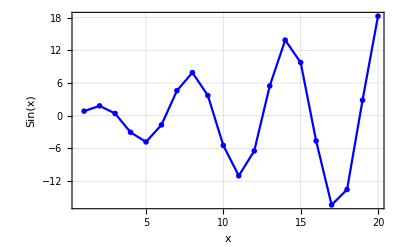

```mathematica
ListLinePlot[datos,
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}
]
```

## Base de Lagrange:

```mathematica
LagrangeBaseElements[xs_,i_]:=Table[If[i≠ j,(x-xs[[j+1]])/(xs[[i+1]]-xs[[j+1]]),1],{j,0,Length[xs]-1}];
LagrangeBase[xs_,i_]:=Apply[Times,LagrangeBaseElements[xs,i]];
```

```mathematica
LagrangeBase[datos[[All,1]],0]
```

((2-x) (3-x) (4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x))/121645100408832000

```mathematica
Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

((2-x) (3-x) (4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x))/121645100408832000+((3-x) (4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-1+x))/6402373705728000+((4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-2+x) (-1+x))/711374856192000+((5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-3+x) (-2+x) (-1+x))/125536739328000+((6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-4+x) (-3+x) (-2+x) (-1+x))/31384184832000

```mathematica
xpand@Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

xpand[((2-x) (3-x) (4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x))/121645100408832000+((3-x) (4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-1+x))/6402373705728000+((4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-2+x) (-1+x))/711374856192000+((5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-3+x) (-2+x) (-1+x))/125536739328000+((6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-4+x) (-3+x) (-2+x) (-1+x))/31384184832000]

```mathematica
LagrangeInterpolate[data_]:=Expand[data[[All,2]].Table[LagrangeBase[data[[All,1]],i],{i,0,Length[data]-1}]];
```

```mathematica
LagrangeInterpolate[datos]
```

-4.28042+15.6346 x-24.1109 x^2+23.9055 x^3-15.4381 x^4+7.0055 x^5-2.39772 x^6+0.635729 x^7-0.131739 x^8+0.0215491 x^9-0.00280737 x^10+0.000291782 x^11-0.0000240227 x^12+1.54529×10^-6 x^13-7.62178×10^-8 x^14+2.81128×10^-9 x^15-7.47874×10^-11 x^16+1.35277×10^-12 x^17-1.48782×10^-14 x^18+7.50715×10^-17 x^19

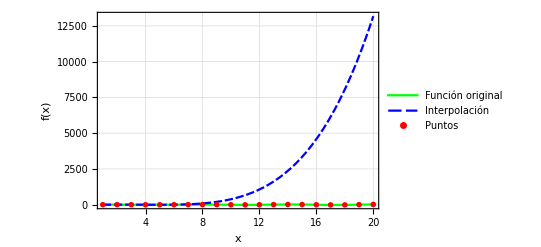

```mathematica
Show[
Plot[
{x Sin[x],0.5964351621647346-2.011191348684978 x+3.486441267683059 x^2-1.3727753574753927 x^3+0.1425612611204672 x^4},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue},PlotLegends->{"Función original","Interpolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

## Comparación con Interopolación Polinomial:

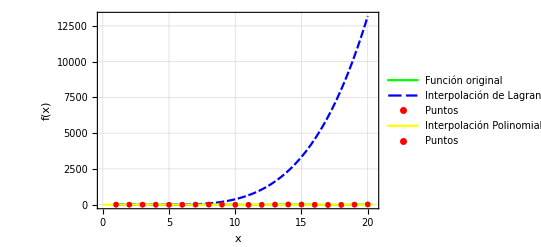

```mathematica
Show[Plot[
{x Sin[x],0.5964351621647346-2.011191348684978 x+3.486441267683059 x^2-1.3727753574753927 x^3+0.1425612611204672 x^4},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue},PlotLegends->{"Función original","Interpolación de Lagrange"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
],
Plot[0.23476803377946487+0.17531612254152584 x+1.260519972854416 x^2-1.2964935742738843 x^3+0.6717387330913387 x^4-0.2747545008801662 x^5+0.08797209116436128 x^6-0.02084311578881154 x^7+0.003704810860377189 x^8-0.0005069090667866576 x^9+0.00005323462030153576 x^10-4.123489541991167*^-6 x^11+2.149933248641468*^-7 x^12-5.540100389107323*^-9 x^13-1.309090885587633*^-10 x^14+1.9037139768001322*^-11 x^15-8.585137314851371*^-13 x^16+2.1391626673307167*^-14 x^17-2.944000422242247*^-16 x^18+1.759388204325254*^-18 x^19,
{x,0,6.5π},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Yellow},PlotLegends->{"Interpolación Polinomial"}],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}]]
```